```mathematica
(*Syntax*)
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
(*No parenthesis are needed*)
∫a[x] b[x] ⅆx+c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
(*But you can use them*)
∫(a[x]+b[x]) ⅆx+c[x]
```

c[x]+∫(a[x]+b[x])ⅆx

```mathematica
(*Superscript*)
x^(a+b)
```

x^(a+b)

```mathematica
(*Sums*)
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
(*Parenthesis for goruping*)
(term)
```

term

```mathematica
(*Square Brackets for functions*)
f[x]
```

```mathematica
(*Curly Brackets for lists*)
{a,b,c}

(*Double brackets for indexing*)
```

```mathematica
v[[i]]
```

```mathematica
(*Lists*)
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
(*Anything can be used in a list*)
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"}
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
(*Lists can contain other lists*)
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[expr,n]
(*attempts to give a result with n-digit precision.*)
```

N::precbd: Requested precision n is not a machine-sized real number between $MinPrecision and $MaxPrecision.

N[expr,n]

```mathematica
N[Sin[2]]
```

0.909297

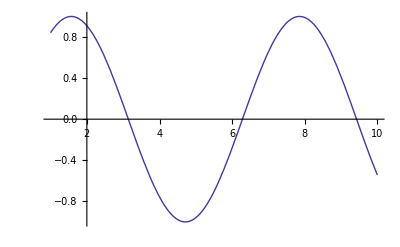

```mathematica
(*Plot a function,with the range of the plot specified in a list*)
Plot[Sin[x],{x,1,10}]
```

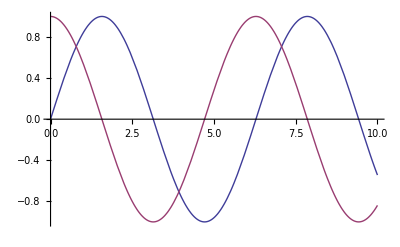

```mathematica
(*Plot 2 functions side by side*)
Plot[{Sin[x],Cos[x]},{x,0,10}]
```

```mathematica
(*SYMBOLIC COMPUTATION*)
(*Numeric*)
3+62-1
```

64

```mathematica
(*Symbolic*)
3 x-x+2
```

2+2 x

```mathematica
(*Mathematica rearranges and combines terms using the standard rules of algebra.*)
```

```mathematica
x y+2 x^2 y+y^2 x^2-2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
(*The function Expand multiplies out products and powers.*)
```

```mathematica
(x+2 y+1) (x-2)^2;
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
(*Factor does essentially the inverse of Expand.*)
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
(*Mathematica knows no rules for this expression,so it leaves the expression in the original form you gave.*)

Log[1+Cos[x]]
```

Log[1+Cos[x]]

```mathematica
(*This uses the transformation rule in the expression.*)
1+2 x/.x->3
```

7

```mathematica
(*expr/.x->value replace x by value in the expression expr*)
(*expr/.{x->xval,y->yval} perform several replacements*)
```

```mathematica
(*This assigns a value to the symbol.*)
t=1+x^2
```

1+x^2

```mathematica
(*This finds the value of,and then replaces by in it.*)
t/.x->2
```

5

```mathematica
(*This finds the value of for a different value of.*)
t/.x->5 a
```

1+25 a^2

```mathematica
(*This finds the value of when is replaced by Pi,and then evaluates the result numerically.*)
t/.x->Pi//N
```

10.8696

```mathematica
(*SIMPLIFYING ALGEBRAIC FUNCTIONS*)
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
(*Differentiating*)
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
(*Simplify that shit*)
Simplify[%]
```

```mathematica
1/(-1+x^4)
```

1/(-1+x^4)

```mathematica
(*CALCULUS*)
(*Partial deriv*)
D[f,x] (*Deriv of f w/respect to x*)
D[f,x,y,...] (*Deriv of f w/respect to x then y etc*)
D[f,{x,n}] (*Nth deriv*)
```

0

```mathematica
(*You can differentiate with respect to any expression that does not involve explicit mathematical operations.*)
D[x[1]^2+x[2]^2,x[1]]
```

2 x[1]

```mathematica
(*INTEGRATION*)
```

```mathematica
Integrate[1/(x^4-a^4),x]
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

```mathematica
(*Definite Integral*)
Integrate[f,{x,xmin,xmax}]
```

f (xmax-xmin)

```mathematica
Integrate[Exp[-x^2],{x,0,Infinity}]
```

(√π)/2

```mathematica
(*Indefinite Integrals*)
Integrate[x^2,x]
```

x^3/3

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
Simplify[D[%,x]]
```

1/(-1+x^2)

```mathematica
(*Differential Equations*)
DSolve[y'[x]+y[x]==1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
(*Something tells me that we won't use differential equations in 202...*)


(*PLOTTING*)
```

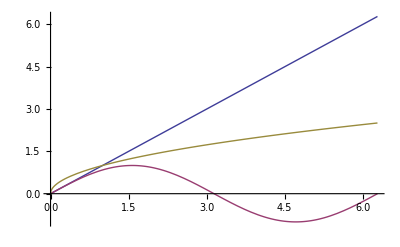

```mathematica
(*Plot several f'ns*)
Plot[{x,Sin[x],Sqrt[x]},{x,0,2 Pi}]
```

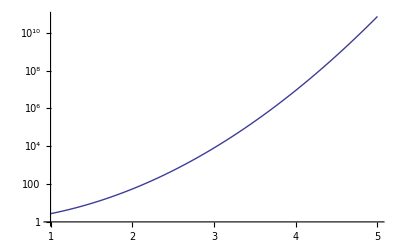

```mathematica
(*Log scaled vert axis*)
LogPlot[E^x^2,{x,1,5}]
```

```mathematica
(*3D parametric*)
ParametricPlot3D[{5 Cos[u],5 Sin[u],u+Sin[u]},{u,-2 Pi,2 Pi}]
```

-Graphics3D-

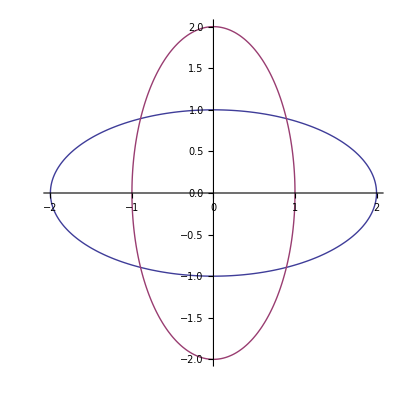

```mathematica
(*Parametric F'ns*)
ParametricPlot[{{2 Sin[t],Cos[t]},{Sin[t],2 Cos[t]}},{t,0,2 Pi}]
```

```mathematica
(*NDSolve*)
(*NDSolve solves a differential equation numerically.It returns solutions in a form that can be readily used in many different ways.One typical use would be to produce a plot of the solution.*)
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1}
```

{Sin[y[x]]+y''[x]==0,y[0]==2,y'[0]==1}

{{y→InterpolatingFunction[{{-10.,10.}},<>]}}

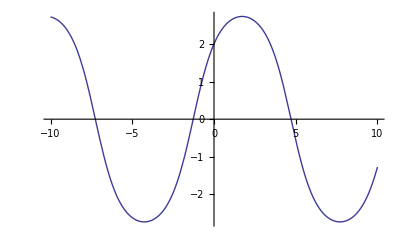

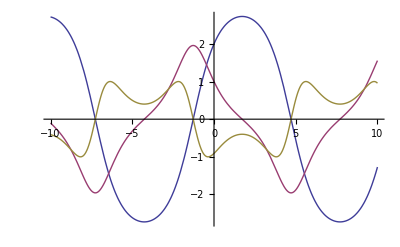

```mathematica
sol=NDSolve[ode1,y,{x,-10,10}]
Plot[y[x]/.sol,{x,-10,10}]
Plot[Evaluate[{y[x],y'[x],y''[x]}/.sol],{x,-10,10}]
```

```mathematica
(*MANIPULATING*)
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20}]
```

```mathematica
(*To view value*)
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},PlotRange->2],{n1,1,20},{n2,1,20}]
```

```mathematica
(*Fortunately it is trivial to add an explicit step size of 1 to the Manipulate command,yielding exactly the same set of possible values in Manipulate as is returned by Table.*)
```

```mathematica
Manipulate[n,{n,1,20,1}]
```

```mathematica
(*You can even use end points and step sizes that are symbolic expressions rather than just plain numbers.*)
Manipulate[Row[{n,"+",m,"=",n+m}],{n,a,10 a,a/12},{m,a,10 a,a/12}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}}]
```

```mathematica
(*Setting initial values*)
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{{a1,1},0,1},{p1,0,2 Pi},{{n2,5/4},1,4},{{a2,1},0,1},{p2,0,2 Pi}]
```

```mathematica
(*Usings Labels*)
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi}]
```

```mathematica
(*Moving control panel location*)
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{a1,1,"Amplitude 1"},0,1},{{p1,0,"Phase 1"},0,2 Pi},{{n2,5/4,"Frequency 2"},1,4},{{a2,1,"Amplitude 2"},0,1},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
(*Control Panel Dividing lines*)
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{{n1,1,"Frequency 1"},1,4},{{n2,5/4,"Frequency 2"},1,4},Delimiter,{{a1,1,"Amplitude 1"},0,1},{{a2,1,"Amplitude 2"},0,1},Delimiter,{{p1,0,"Phase 1"},0,2 Pi},{{p2,0,"Phase 2"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
(*Control Panel descriptions and text style*)
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],Style["Horizontal",12,Bold],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,Style["Vertical",12,Bold],{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```